Plots for ps1 problem 6 a,b,c

```mathematica
<< peeters`;
peeters`setGitDir["../project/figures/ece1505-convex-optimization"]
```

/Users/pjoot/project/figures/ece1505-convex-optimization

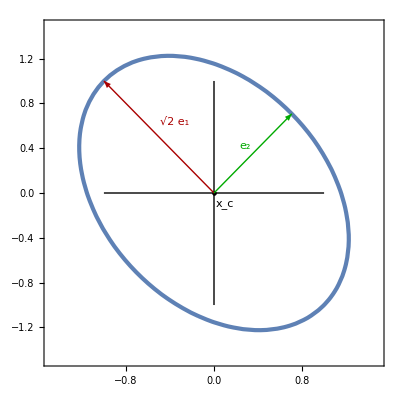

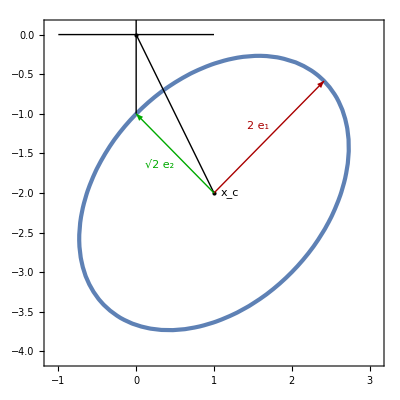

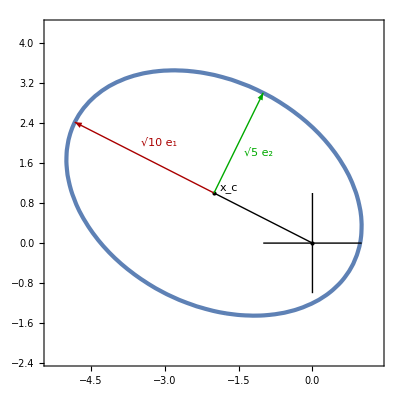

```mathematica
ClearAll[plot, bold, larger, pa,pb,pc]
bold := Style[#, Bold] &;
larger := Style[#, Larger] & ;

plot[xc_List, p_List, s_,fc_,f1_,f2_] := Module[{q,d,r,x0,y0,paxis,e1,e2,a1,a2}, 
{d,q} = Eigensystem[p]; 
paxis = Sqrt[#] &/@ d ;
{a1,a2} = paxis;
r = s(paxis// Max);
q = Normalize[#] &/@ q;
{x0,y0} = xc;
{e1,e2} = (q (*// Transpose*));
Show[{
ContourPlot[ 1 == ({x,y}-xc).(Inverse[p].({x,y}-xc)),
{x,x0-r,x0+r},
 {y,y0-r,y0+r},
PlotTheme-> "ThickLines"
],
Graphics[{
PointSize[Large],
Point[xc],
Line[{{0,0},xc}],
Line[{{-1,0},{1,0}}],
Line[{{0,-1},{0,1}}],
Text[larger[Subscript[bold["x"], c] ],xc +fc],
Point[{0,0}],
Thick,
Red// Darker,
Arrow[{xc,xc+a1 e1}],
Text[a1 larger[Subscript[bold["e"], 1]],xc+a1 e1/2 + f1],
Green // Darker,
Arrow[{xc,xc+a2 e2}],
Text[a2 larger[Subscript[bold["e"], 2]],xc+a2 e2/2 + f2]
}
]
}]
];
pa =plot[{0,0},{{3/2,-1/2},{-1/2,3/2}},1.05,0.1{1,-1},0.2{.7,.7},0.1{-.7,.7}]
pb =plot[{1,-2},{{3,1},{1,3}},1.05,0.2{1,0},0.2{-.7,.7},-0.2{1,.7}]
pc =plot[{-2,1},{{9,-2},{-2,6}},1.05,0.2{1.5,0.5},0.3{1,1},0.4{1,-0.5}]
```

```mathematica
peeters`exportForLatex[ "ps1p6aFig2", pa]
peeters`exportForLatex[ "ps1p6bFig3", pb]
peeters`exportForLatex[ "ps1p6cFig4", pc]
```

{ps1p4aFig2.eps,ps1p4aFig2pn.png}

{ps1p4bFig3.eps,ps1p4bFig3pn.png}

{ps1p4cFig4.eps,ps1p4cFig4pn.png}